# Tweets of the US Senators of the 115th Congress

Source: https://dataverse.harvard.edu/file.xhtml?fileId=3354806&version=3.0

Set options used for all ListPlots in this notebook:

```mathematica
SetOptions[ListPlot,PlotTheme->"Detailed",ImageSize->Large,PlotRange->All];
SetOptions[DateListPlot,PlotTheme->"Detailed",ImageSize->Large,PlotRange->All];
```

Set the directory:

```mathematica
SetDirectory@NotebookDirectory[]
```

D:\github\tweets-115th-congress

Get the files:

```mathematica
files=Apply[Join,FileNames["*.json",FileNameJoin[{"US115thcongress",#}]]&/@{"Democrat","Republican","Independent"}]
```

{US115thcongress\Democrat\amyklobuchar_twitter.json,US115thcongress\Democrat\brianschatz_twitter.json,US115thcongress\Democrat\ChrisCoons_twitter.json,US115thcongress\Democrat\ChrisMurphyCT_twitter.json,US115thcongress\Democrat\ChrisVanHollen_twitter.json,US115thcongress\Democrat\clairecmc_twitter.json,US115thcongress\Democrat\CoryBooker_twitter.json,US115thcongress\Democrat\MarkWarner_twitter.json,US115thcongress\Democrat\MartinHeinrich_twitter.json,US115thcongress\Democrat\maziehirono_twitter.json,US115thcongress\Democrat\PattyMurray_twitter.json,US115thcongress\Democrat\RonWyden_twitter.json,US115thcongress\Democrat\SenatorBaldwin_twitter.json,US115thcongress\Democrat\SenatorCantwell_twitter.json,US115thcongress\Democrat\SenatorCardin_twitter.json,US115thcongress\Democrat\SenatorCarper_twitter.json,US115thcongress\Democrat\SenatorDurbin_twitter.json,US115thcongress\Democrat\SenatorHassan_twitter.json,US115thcongress\Democrat\SenatorHeitkamp_twitter.json,US115thcongress\Democrat\SenatorLeahy_twitter.json,US115thcongress\Democrat\SenatorMenendez_twitter.json,US115thcongress\Democrat\SenatorShaheen_twitter.json,US115thcongress\Democrat\SenatorTester_twitter.json,US115thcongress\Democrat\SenatorTomUdall_twitter.json,US115thcongress\Democrat\SenBennetCO_twitter.json,US115thcongress\Democrat\SenBillNelson_twitter.json,US115thcongress\Democrat\SenBlumenthal_twitter.json,US115thcongress\Democrat\SenBobCasey_twitter.json,US115thcongress\Democrat\SenCortezMasto_twitter.json,US115thcongress\Democrat\SenDonnelly_twitter.json,US115thcongress\Democrat\SenDougJones_twitter.json,US115thcongress\Democrat\SenDuckworth_twitter.json,US115thcongress\Democrat\SenFeinstein_twitter.json,US115thcongress\Democrat\SenGaryPeters_twitter.json,US115thcongress\Democrat\SenGillibrand_twitter.json,US115thcongress\Democrat\SenJackReed_twitter.json,US115thcongress\Democrat\SenJeffMerkley_twitter.json,US115thcongress\Democrat\Sen_JoeManchin_twitter.json,US115thcongress\Democrat\SenKamalaHarris_twitter.json,US115thcongress\Democrat\senmarkey_twitter.json,US115thcongress\Democrat\SenSchumer_twitter.json,US115thcongress\Democrat\SenSherrodBrown_twitter.json,US115thcongress\Democrat\SenStabenow_twitter.json,US115thcongress\Democrat\SenTinaSmith_twitter.json,US115thcongress\Democrat\SenWarren_twitter.json,US115thcongress\Democrat\SenWhitehouse_twitter.json,US115thcongress\Democrat\timkaine_twitter.json,US115thcongress\Republican\BenSasse_twitter.json,US115thcongress\Republican\BillCassidy_twitter.json,US115thcongress\Republican\BobCorker_twitter.json,US115thcongress\Republican\ChuckGrassley_twitter.json,US115thcongress\Republican\GrahamBlog_twitter.json,US115thcongress\Republican\JeffFlake_twitter.json,US115thcongress\Republican\JerryMoran_twitter.json,US115thcongress\Republican\jiminhofe_twitter.json,US115thcongress\Republican\JohnBoozman_twitter.json,US115thcongress\Republican\JohnCornyn_twitter.json,US115thcongress\Republican\joniernst_twitter.json,US115thcongress\Republican\lisamurkowski_twitter.json,US115thcongress\Republican\marcorubio_twitter.json,US115thcongress\Republican\MikeCrapo_twitter.json,US115thcongress\Republican\RandPaul_twitter.json,US115thcongress\Republican\RoyBlunt_twitter.json,US115thcongress\Republican\SenAlexander_twitter.json,US115thcongress\Republican\SenateMajLdr_twitter.json,US115thcongress\Republican\SenatorBurr_twitter.json,US115thcongress\Republican\SenatorCollins_twitter.json,US115thcongress\Republican\SenatorEnzi_twitter.json,US115thcongress\Republican\SenatorFischer_twitter.json,US115thcongress\Republican\SenatorIsakson_twitter.json,US115thcongress\Republican\SenatorLankford_twitter.json,US115thcongress\Republican\SenatorRisch_twitter.json,US115thcongress\Republican\SenatorRounds_twitter.json,US115thcongress\Republican\SenatorTimScott_twitter.json,US115thcongress\Republican\SenatorWicker_twitter.json,US115thcongress\Republican\SenCapito_twitter.json,US115thcongress\Republican\SenCoryGardner_twitter.json,US115thcongress\Republican\SenDanSullivan_twitter.json,US115thcongress\Republican\SenDavidPerdue_twitter.json,US115thcongress\Republican\SenDeanHeller_twitter.json,US115thcongress\Republican\SenJohnBarrasso_twitter.json,US115thcongress\Republican\SenJohnHoeven_twitter.json,US115thcongress\Republican\SenJohnKennedy_twitter.json,US115thcongress\Republican\SenJohnThune_twitter.json,US115thcongress\Republican\SenJonKyl_twitter.json,US115thcongress\Republican\SenMikeLee_twitter.json,US115thcongress\Republican\SenOrrinHatch_twitter.json,US115thcongress\Republican\SenPatRoberts_twitter.json,US115thcongress\Republican\SenRobPortman_twitter.json,US115thcongress\Republican\SenRonJohnson_twitter.json,US115thcongress\Republican\SenShelby_twitter.json,US115thcongress\Republican\SenTedCruz_twitter.json,US115thcongress\Republican\SenThadCochran_twitter.json,US115thcongress\Republican\SenThomTillis_twitter.json,US115thcongress\Republican\SenToddYoung_twitter.json,US115thcongress\Republican\SenTomCotton_twitter.json,US115thcongress\Republican\SenToomey_twitter.json,US115thcongress\Republican\SteveDaines_twitter.json,US115thcongress\Independent\SenAngusKing_twitter.json,US115thcongress\Independent\SenatorSanders_twitter.json}

Check for the number of senators that have tweeted:

```mathematica
Length[files]
```

100

Import the twitter archive for each senator:

```mathematica
dataset=Dataset[Association[StringReplace[FileBaseName[#],"_twitter"->""]->Dataset[Map[Association,Import[#]]]&/@files]];
```

Display a twitter archive for a randomly chose senator:

```mathematica
RandomChoice[dataset]
```

Dataset[<>]

Get the dataset for a specific senator

```mathematica
dataset["SteveDaines"]
```

Dataset[<>]

#### Who tweeted the most?

Get the number of tweets and sort them:

```mathematica
numberTweets=dataset[ReverseSort,Length]
```

Dataset[<>]

The most frequent tweeters:

```mathematica
Take[numberTweets,5]
```

Dataset[<>]

The least frequent tweeters:

```mathematica
Take[numberTweets,-5]
```

Dataset[<>]

Due to an error in the source data, senator Sanders only has one tweet (pointing to the correct @SenSanders twitter handle):

```mathematica
dataset["SenatorSanders"]
```

Dataset[<>]

Plot the number of tweets so they are easy to compare:

```mathematica
ListPlot[numberTweets]
```

-Graphics-

#### Who has the most ‘likes’ ?

Compute the ‘likes’ for one senator. Use ToExpression to turn the ‘likes’ strings into integers

```mathematica
dataset["SenWhitehouse"][Total[Map[ToExpression,#]]&,"likes"]
```

1747155

Compute the number of ‘likes’ for each senator and sort them:

```mathematica
numberLikes=ReverseSort@Map[#[Total[Map[ToExpression,#]]&,"likes"]&,dataset]
```

Dataset[<>]

The senators with the most ‘likes’:

```mathematica
Take[numberLikes,5]
```

Dataset[<>]

The senators with the least ‘likes’:

```mathematica
Take[numberLikes,-5]
```

Dataset[<>]

```mathematica
ListPlot[numberLikes]
```

-Graphics-

#### Who has the most ‘retweets’ ?

Compute the ‘retweets’ for one senator. Use ToExpression to turn the ‘likes’ strings into integers

```mathematica
dataset["brianschatz"][Total[Map[ToExpression,#]]&,"retweets"]
```

2096478

Compute the number of ‘retweets’ for each senator and sort them:

```mathematica
numberRetweets=ReverseSort@Map[#[Total[Map[ToExpression,#]]&,"retweets"]&,dataset]
```

Dataset[<>]

The senators with the most ‘retweets’:

```mathematica
Take[numberRetweets,5]
```

Dataset[<>]

The senators with the least ‘retweets’:

```mathematica
Take[numberRetweets,-5]
```

Dataset[<>]

Plot the ‘retweets’ for each senator:

```mathematica
ListPlot[numberRetweets]
```

-Graphics-

#### Who has the most ‘replies’ ?

Compute the ‘replies’ for one senator. Use ToExpression to turn the ‘likes’ strings into integers

```mathematica
dataset["SenateMajLdr"][Total[Map[ToExpression,#]]&,"retweets"]
```

403353

Compute the number of ‘replies’ for each senator and sort them:

```mathematica
numberReplies=ReverseSort@Map[#[Total[Map[ToExpression,#]]&,"replies"]&,dataset]
```

Dataset[<>]

The senators with the most ‘replies’:

```mathematica
Take[numberReplies,5]
```

Dataset[<>]

The senators with the least ‘replies’:

```mathematica
Take[numberReplies,-5]
```

Dataset[<>]

Plot the ‘replies’ for each senator:

```mathematica
ListPlot[numberReplies]
```

-Graphics-

#### What are the total number of tweets per day?

Get the daily counts of tweets for all senators combined:

```mathematica
counts=KeySort[Counts@Map[StringTake[#,10]&,Join@@Values[Normal[Map[Normal[#[All,"timestamp"]]&,dataset]]]]];
```

Plot the number of tweets per day. The number of tweets has grown over time (a lot). Tweets before the actual start date of the 115th Congress are older tweets that were retweeted.

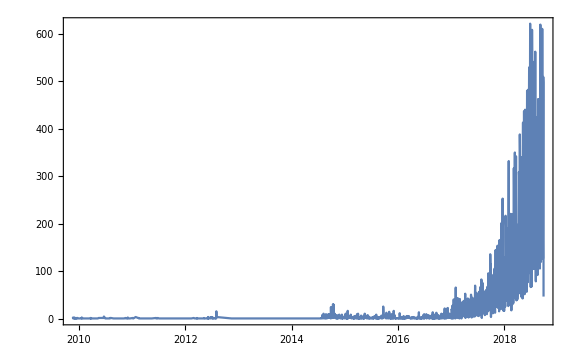

```mathematica
DateListPlot[counts]
```

Plot the moving average of tweets per senator per day. Note the increase from almost zero to about 3 at the end of the time period:

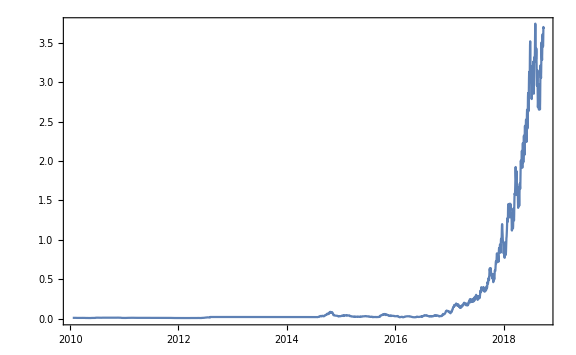

```mathematica
DateListPlot[MovingAverage[counts/100.0,25],ImageSize->Large]
```

#### What are the most used #HashTags?

Get the hashtags used by each senator and tally them by their frequency of use:

```mathematica
hashtags=Map[#[ReverseSort@Counts@Flatten@StringCases[#,"#"~~WordCharacter..]&,"text"]&,dataset];
```

Look at the results for a few senators:

```mathematica
RandomSample[hashtags,3]
```

Dataset[<>]

Overall hashtag frequency:

```mathematica
allHashtags=ReverseSort@Counts@Flatten@Map[Flatten@StringCases[#,"#"~~WordCharacter..]&,tweetText];
```

Most popular, showing common topics such as the tax reform bill, net neutrality, supreme court, farm bill, the state of the union, and the deferred action for childhood arrivals policy:

```mathematica
Dataset@Take[allHashtags,100]
```

Dataset[<>]

A word cloud of the most popular hashtags

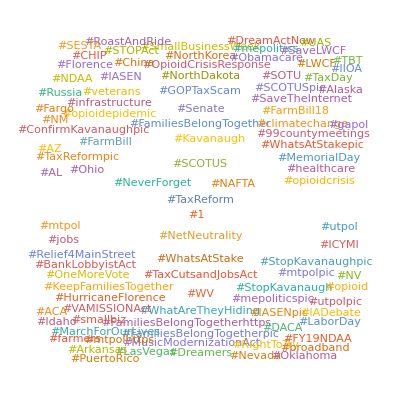

```mathematica
WordCloud[Take[allHashtags,100]]
```

Plot all the top 1000  hashtags by their frequency:

```mathematica
ListPlot[Take[allHashtags,1000]]
```

-Graphics-